```mathematica
<<HypothesisTesting`

dec={-3.2 ,-5.3 ,0.1 ,-1.8 ,-0.5 ,-0.6 ,1,-2.6 ,-7.6 ,-1,-0.8 ,-7.2 ,-2.9 ,-1.7 ,0.1 ,-5.5 ,-4.6 ,-7.4 ,0.5 ,-3,-3.6 ,-4.2 ,0.6 ,-4,-1.5 ,-2,-1.6 ,-2.3 ,-2.8 ,0.5 ,-1.5 ,-3,0,-4.6 ,0.2 ,0.3 ,-1.7 ,-1.8 ,0.3 ,0.1 ,-2.4 ,-1.1 ,-3.7 ,-4.4 ,-0.6 ,-2.2 ,0,-2.4 ,-3.3 ,-0.8 ,-1,0.3 ,1.4 ,1.8 ,-2.1 ,2.2 ,-7,-0.7 ,-2.4 ,-1.2 ,-3.3 ,-0.9 ,-1,-0.5 ,-3.9 ,2.4 ,-4.5 ,-2.9 ,-5.5 ,-1.2 ,3,0.8 ,-1.8 ,2.3 ,-3.1 ,2.6 ,0.2 ,2.7 ,-3.9 ,-0.5 ,-2.8 ,-2.7 ,-2.7 ,-0.1 ,0.3 ,1.4 ,-1.4 ,-0.3 ,-2,2.3 ,1,-1.1 ,2,-1.7 ,1.9 ,1.6 ,-3.2 ,-0.3 ,-0.9 ,-1.6 ,-0.1 ,1.2 ,-3.4 ,-3.2 ,-1.8 ,-0.9 ,-4,-0.4 ,-4.6 ,-1.5 ,-4,-0.8 ,1.1 ,3.3 ,-2.5 ,1.2 ,0.7 ,-2.6 ,-0.1 ,-6,-1.7 ,-0.8 ,-5.7 ,0.3 ,-1.1 ,0.8 ,-4.3 ,-1.5 ,-1.5 ,-2.4 ,-2.2 ,0.8 ,0.6 ,1,-0.4 ,1.8 ,-4.9 ,-3.2 ,-0.5 ,-0.4 ,-1.6 ,2.3 ,-2,-4,0.9 ,1,-0.5 ,4.3 ,1.2 ,0.9 ,-2,-7.2 ,1.9 ,-3.6 ,2.8 ,-0.1 ,3.5 ,1.6 ,0.9 ,0.2 ,2.4 ,3.4 };
jan = {0.2 ,-1.8 ,-8.6 ,-7.2 ,0.9 ,-4.1 ,-2.7 ,1.4 ,-9.4 ,-5.5 ,-2.1 ,-1.1 ,-5.2 ,-0.1 ,1.8 ,1.2 ,-9.3 ,-3.6 ,-4.6 ,-2.9 ,-5.4 ,-3.3 ,-7.7 ,0.9 ,-3.5 ,-1.6 ,-4.5 ,-3.6 ,-1.2 ,-3.8 ,-1.8 ,0.3 ,-5.1 ,-6,-7.9 ,-1.3 ,-5.8 ,-2.5 ,-5.2 ,0.9 ,-4.1 ,-3.2 ,-3.6 ,-1.6 ,-3.6 ,-0.5 ,-3.4 ,-1,-4.1 ,-2.3 ,-1.5 ,-1.8 ,-1.4 ,-5.4 ,-3.2 ,-3.6 ,-4.7 ,-1.9 ,-8.1 ,-5.7 ,-1.5 ,-3.3 ,-1.8 ,-5.7 ,-0.7 ,-4,0.5 ,-3.8 ,-1.7 ,-3.1 ,-4.5 ,1.6 ,-3.5 ,1,-2.4 ,0,-2.5 ,-1.6 ,-1.7 ,-1.5 ,-1.5 ,-7.4 ,-10.9 ,-11.2 ,-3.8 ,-1.9 ,-2.7 ,-2.5 ,-4.3 ,-5.4 ,-0.1 ,-5,-3.4 ,-1.8 ,-3.2 ,-4.8 ,-3.4 ,-4.6 ,-0.5 ,-4.1 ,-4.4 ,-4.6 ,-2.7 ,-2,-7.7 ,-2,-2,-7.3 ,-5.3 ,-7,-3,-7.6 ,-1.2 ,-3.8 ,0.7 ,0.2 ,1.1 ,-5.1 ,-2.2 ,-1.5 ,-7.1 ,-4.7 ,-4,-7.2 ,0.7 ,-3,-9,-5,-12,-0.1 ,2.4 ,0.5 ,-0.7 ,0.6 ,-0.3 ,-2.1 ,-2.5 ,-4,-2.3 ,-0.3 ,-2.3 ,-1,-0.7 ,-1.1 ,-3.9 ,-3.5 ,0.6 ,-3.1 ,-0.3 ,1.4 ,-1.9 ,-7.8 ,-2.6 ,-1.7 ,-4,-2.2 ,0.1 ,-5,-1,-0.6 ,-2.5 ,3.3 };
feb ={0.1 ,-6.2 ,-1.3 ,-6.8 ,0.9 ,-1.6 ,-8.8 ,-3,-2,-1.5 ,-0.5 ,-7.1 ,-12.2 ,-1.5 ,-2.4 ,-1.3 ,-5.9 ,-4.3 ,-5.5 ,-0.5 ,-7,-0.9 ,-8,-1.3 ,-1.3 ,-1.5 ,-1.5 ,-3.8 ,-0.6 ,-7.6 ,-7.2 ,-1.9 ,-0.5 ,-4.9 ,-11,-0.7 ,-8.2 ,-0.8 ,-4.2 ,-2.2 ,-2.5 ,-7.6 ,-6.7 ,-5,0.5 ,-4.9 ,-1.4 ,-1.2 ,-3,-1.6 ,-5.2 ,-0.2 ,-2.1 ,-4.2 ,-0.5 ,1.4 ,-2.1 ,-2.4 ,-5.2 ,-2.1 ,-4.6 ,0.3 ,-1.9 ,-4.5 ,-5.7 ,-6.9 ,0.5 ,-5,-2.1 ,-2.5 ,-9.1 ,-1.9 ,-3.8 ,-2.9 ,-3.6 ,0.1 ,-1.2 ,-5.1 ,-3.5 ,0.4 ,1.6 ,-10.8 ,-6.6 ,-11.1 ,1.3 ,-1.5 ,-1.1 ,-5.1 ,-10.7 ,-3.3 ,0.8 ,-1.7 ,-1.9 ,-2.4 ,-4.3 ,-6,-5.2 ,-9.2 ,-1.6 ,-6.7 ,-1.6 ,-5.2 ,0.4 ,-2.8 ,-7.8 ,-4.3 ,-4.7 ,-10.9 ,-1.6 ,-4,-6,-10.7 ,-1.9 ,-1,-0.7 ,0.6 ,-1.2 ,-2.1 ,-5,-6.3 ,-6.2 ,-6.2 ,-2.7 ,-4,-3.8 ,-1.7 ,-11.6 ,-8.4 ,-4.4 ,-0.9 ,2.4 ,3.4 ,-3.1 ,-0.1 ,-0.9 ,-6.9 ,0.1 ,-6.9 ,-0.5 ,0.8 ,-2.4 ,-0.4 ,-4.2 ,0.9 ,-4,-1.6 ,-2.5 ,-3.5 ,-3.6 ,2.1 ,-2.6 ,-6.1 ,-5.1 ,-3.7 ,-2.1 ,1.5 ,0.4 ,-0.3 ,-0.7 ,-4.1 ,1,2};
mar={0.7 ,-2.7 ,-0.2 ,-4.4 ,-0.2 ,-1.9 ,-4.2 ,-5.8 ,-5,0.1 ,-2.1 ,-2.3 ,1.8 ,-0.9 ,-0.6 ,-0.5 ,-3,-2.1 ,-4.9 ,-1.1 ,-3.1 ,-0.6 ,-6.2 ,1.2 ,-4.4 ,0.3 ,-1,-3,-0.3 ,-8.9 ,-4.3 ,0.4 ,-2.4 ,-2,-0.5 ,2.8 ,-2.8 ,0.1 ,-1.8 ,-1.3 ,-3.5 ,-2.9 ,-2,-2.8 ,3.4 ,-2.1 ,0.2 ,-2,0.1 ,-2.1 ,-2.3 ,1.3 ,0.2 ,1.2 ,1.8 ,-0.7 ,-4,-2.8 ,-6,-0.1 ,-2.3 ,2.9 ,3.4 ,-1.5 ,-0.5 ,-3.9 ,-2.7 ,-0.4 ,1.4 ,-2,0.2 ,0.6 ,-4.3 ,-2.6 ,0.8 ,0.2 ,-0.4 ,0.3 ,-2.3 ,3.6 ,-0.4 ,-5.5 ,-3.1 ,-7.2 ,2.4 ,-1.1 ,1.3 ,-1.4 ,-5.1 ,1.7 ,-0.6 ,0.9 ,-3.5 ,-3.7 ,2.6 ,0,-3.5 ,-1.6 ,-2.3 ,-5.5 ,2.2 ,-1.5 ,3,-4.1 ,-4.4 ,-2.3 ,-1.4 ,-1.3 ,2.6 ,0.8 ,-4,-1.6 ,-2.8 ,0.2 ,2.9 ,0.8 ,0.9 ,-2.9 ,0.4 ,-1.6 ,-1.1 ,-3.1 ,-2.2 ,1.1 ,-0.1 ,-2,-1.7 ,0.2 ,-4.2 ,-2.1 ,2.6 ,3.9 ,1.4 ,2,1,-0.1 ,1.3 ,-1.5 ,1.6 ,-0.5 ,0.7 ,1.2 ,-1.3 ,1.6 ,2.3 ,0.9 ,-2.3 ,-3.8 ,3.8 ,0.8 ,0.1 ,-1.1 ,0.3 ,3.5 ,-3.2 ,3.6 ,3,2.3 ,2.4 ,-2.5 ,1.8 ,2.7 };
apr={2.2 ,3.4 ,2.2 ,2.9 ,3.8 ,2.3 ,4.3 ,3.9 ,0.5 ,3.4 ,5.8 ,5.4 ,0.6 ,3.9 ,2.4 ,3.6 ,1.3 ,3.7 ,-0.2 ,5,1,4,0.5 ,3.6 ,2.5 ,2.3 ,3.7 ,4.5 ,3.9 ,-0.3 ,2.1 ,3.7 ,2.6 ,2.9 ,4,5.9 ,4,3.4 ,3.7 ,1.9 ,3.3 ,2.6 ,3.9 ,0.4 ,2.6 ,3.8 ,1.7 ,5.2 ,2.3 ,2.5 ,1.3 ,4.7 ,4,3.2 ,4.7 ,6.4 ,3.9 ,4.8 ,0.6 ,3.7 ,3.1 ,4.9 ,6.7 ,1.6 ,1.9 ,1.2 ,5.6 ,3.3 ,2.6 ,3.5 ,0.6 ,5.1 ,1.4 ,3.3 ,3.2 ,5.2 ,4.3 ,3.2 ,4.8 ,4.3 ,4.6 ,2.3 ,1.2 ,3.8 ,6.4 ,2.3 ,4.8 ,5.7 ,4.6 ,6.1 ,5.1 ,5.2 ,4.1 ,5.9 ,5.9 ,2.4 ,1,0.8 ,3.1 ,1.8 ,5.1 ,3.4 ,5.1 ,4.1 ,3.3 ,5.2 ,3.2 ,0.7 ,4.2 ,6.4 ,3.9 ,1.7 ,2.7 ,3.1 ,3.1 ,5.4 ,3.8 ,3.5 ,2.3 ,2.6 ,2.8 ,4.8 ,3.9 ,4.1 ,4,5.3 ,1.6 ,2.1 ,4.1 ,3.1 ,4.6 ,6.5 ,4.8 ,2.6 ,5.2 ,5.9 ,3.3 ,5.6 ,3.1 ,3.1 ,6.6 ,6,5,6.5 ,3.7 ,6,6,4.5 ,7.3 ,6.5 ,7.6 ,5.5 ,8.3 ,4,4,6.6 ,6.5 ,5.3 ,4,6.2 ,6.5 ,6.2 };
maj={9.7 ,7.4 ,5.9 ,10.2 ,8.1 ,5.1 ,10.8 ,7,3.4 ,10.4 ,7.4 ,8.9 ,6.2 ,10.3 ,5.8 ,6.3 ,9.8 ,5.6 ,5.6 ,8.7 ,8.5 ,8.4 ,7.8 ,9.4 ,8.8 ,7.6 ,6.4 ,8.7 ,8.7 ,7.5 ,11.9 ,11,8.8 ,8.2 ,7.1 ,9,11.7 ,8.2 ,10.2 ,8.7 ,7,6.8 ,10.1 ,5.8 ,9.2 ,7.1 ,9.7 ,10.6 ,7.2 ,7.8 ,5.2 ,9.7 ,10.5 ,7.2 ,9.5 ,9,7.4 ,7.9 ,8.6 ,9.6 ,9.8 ,10.3 ,12.4 ,9.7 ,7.4 ,8.7 ,9.5 ,8,5.6 ,7.8 ,8.9 ,10.3 ,9.4 ,8.8 ,7.6 ,11.2 ,7.2 ,9.3 ,12.2 ,8.9 ,9.1 ,10.2 ,7.8 ,7.5 ,10.5 ,7.8 ,8.6 ,9.1 ,11.9 ,9.8 ,11.5 ,10.4 ,7.2 ,7.7 ,9.3 ,10.4 ,6.6 ,10.3 ,7.9 ,8.6 ,9.5 ,10.1 ,8.6 ,7.3 ,11.3 ,10.8 ,7.4 ,9.4 ,8,7.3 ,8.1 ,8.9 ,10.4 ,8.8 ,9.7 ,8.2 ,10.3 ,9.7 ,8.9 ,8.9 ,9.8 ,7.8 ,10.8 ,9.4 ,10.2 ,10.9 ,9,11.5 ,7.5 ,11.2 ,11.5 ,10.8 ,7.2 ,12.6 ,12.6 ,8.6 ,8.1 ,7.6 ,8.2 ,9.8 ,8.9 ,11.1 ,9.9 ,11.4 ,10.3 ,9.6 ,9.7 ,10.1 ,10.2 ,10.7 ,10.7 ,10.1 ,10.6 ,10.9 ,11.9 ,9.9 ,8.9 ,11.9 ,10.1 ,14.8 ,9.6 ,8.8 };
```

```mathematica
viMedel= Total[Flatten[{dec,jan,feb}]]/Length[Flatten[{dec,jan,feb}]]
vin=Length[Flatten[{dec,jan,feb}]]
viMånader = Flatten[{dec,jan,feb}];
summaVi = Total[viMånader]
Sort[viMånader][[1]]
Sort[viMånader][[Length[viMånader]]]
"Konfidensintervallet år 95%, signifikansnivå på 5%";
percentil =  0.05
Sort[viMånader]
```

-2.48313

486

-1206.8

-12.2

4.3

0.05

{-12.2,-12,-11.6,-11.2,-11.1,-11,-10.9,-10.9,-10.8,-10.7,-10.7,-9.4,-9.3,-9.2,-9.1,-9,-8.8,-8.6,-8.4,-8.2,-8.1,-8,-7.9,-7.8,-7.8,-7.7,-7.7,-7.6,-7.6,-7.6,-7.6,-7.4,-7.4,-7.3,-7.2,-7.2,-7.2,-7.2,-7.2,-7.1,-7.1,-7,-7,-7,-6.9,-6.9,-6.9,-6.8,-6.7,-6.7,-6.6,-6.3,-6.2,-6.2,-6.2,-6.1,-6,-6,-6,-6,-5.9,-5.8,-5.7,-5.7,-5.7,-5.7,-5.5,-5.5,-5.5,-5.5,-5.4,-5.4,-5.4,-5.3,-5.3,-5.2,-5.2,-5.2,-5.2,-5.2,-5.2,-5.1,-5.1,-5.1,-5.1,-5.1,-5,-5,-5,-5,-5,-5,-4.9,-4.9,-4.9,-4.8,-4.7,-4.7,-4.7,-4.6,-4.6,-4.6,-4.6,-4.6,-4.6,-4.6,-4.5,-4.5,-4.5,-4.5,-4.4,-4.4,-4.4,-4.3,-4.3,-4.3,-4.3,-4.3,-4.2,-4.2,-4.2,-4.2,-4.1,-4.1,-4.1,-4.1,-4.1,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-3.9,-3.9,-3.9,-3.8,-3.8,-3.8,-3.8,-3.8,-3.8,-3.8,-3.7,-3.7,-3.6,-3.6,-3.6,-3.6,-3.6,-3.6,-3.6,-3.6,-3.6,-3.5,-3.5,-3.5,-3.5,-3.5,-3.4,-3.4,-3.4,-3.4,-3.3,-3.3,-3.3,-3.3,-3.3,-3.2,-3.2,-3.2,-3.2,-3.2,-3.2,-3.2,-3.1,-3.1,-3.1,-3.1,-3,-3,-3,-3,-3,-3,-2.9,-2.9,-2.9,-2.9,-2.8,-2.8,-2.8,-2.7,-2.7,-2.7,-2.7,-2.7,-2.7,-2.6,-2.6,-2.6,-2.6,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.5,-2.4,-2.4,-2.4,-2.4,-2.4,-2.4,-2.4,-2.4,-2.4,-2.3,-2.3,-2.3,-2.3,-2.2,-2.2,-2.2,-2.2,-2.2,-2.1,-2.1,-2.1,-2.1,-2.1,-2.1,-2.1,-2.1,-2.1,-2,-2,-2,-2,-2,-2,-2,-2,-1.9,-1.9,-1.9,-1.9,-1.9,-1.9,-1.9,-1.9,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.7,-1.7,-1.7,-1.7,-1.7,-1.7,-1.7,-1.7,-1.7,-1.6,-1.6,-1.6,-1.6,-1.6,-1.6,-1.6,-1.6,-1.6,-1.6,-1.6,-1.6,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.4,-1.4,-1.4,-1.3,-1.3,-1.3,-1.3,-1.3,-1.2,-1.2,-1.2,-1.2,-1.2,-1.2,-1.2,-1.1,-1.1,-1.1,-1.1,-1.1,-1.1,-1,-1,-1,-1,-1,-1,-1,-0.9,-0.9,-0.9,-0.9,-0.9,-0.9,-0.8,-0.8,-0.8,-0.8,-0.8,-0.7,-0.7,-0.7,-0.7,-0.7,-0.7,-0.7,-0.6,-0.6,-0.6,-0.6,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.5,-0.4,-0.4,-0.4,-0.4,-0.3,-0.3,-0.3,-0.3,-0.3,-0.3,-0.2,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,-0.1,0,0,0,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.2,0.2,0.2,0.2,0.2,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.4,0.4,0.4,0.5,0.5,0.5,0.5,0.5,0.5,0.6,0.6,0.6,0.6,0.6,0.7,0.7,0.7,0.8,0.8,0.8,0.8,0.8,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,1,1,1,1,1,1,1.1,1.1,1.2,1.2,1.2,1.2,1.3,1.4,1.4,1.4,1.4,1.4,1.5,1.6,1.6,1.6,1.6,1.8,1.8,1.8,1.9,1.9,2,2,2.1,2.2,2.3,2.3,2.3,2.4,2.4,2.4,2.4,2.6,2.7,2.8,3,3.3,3.3,3.4,3.4,3.5,4.3}

```mathematica
våMedel= Total[Flatten[{mar,apr,maj}]]/Length[Flatten[{mar,apr,maj}]]
vån  =Length[Flatten[{mar,apr,maj}]]
våMånader = Flatten[{mar,apr,maj}];
minstaEleVå =Sort[våMånader][[1]]
störstaEleVå = Sort[våMånader][[Length[våMånader]]]Mars, April, Maj 
lägst: -8.9
högst: 14.8

December, Januari, Februari
lägst: -12.2
högst: 4.3 
summaVå = Total[våMånader]
Sort[våMånader]
```

3.97922

486

-8.9

```mathematica
"Hitta element inom ett spann med månaderna mar, apr, maj åren 1859-2020" ;
k1 = Length[Select[våMånader,#<-6&]]
k2 = Length[Select[våMånader,-3>#>=-6&]]
k3 = Length[Select[våMånader,0>#>=-3&]]
k4 = Length[Select[våMånader,3>#>=0&]]
k5 = Length[Select[våMånader,6>#>=3&]]
k6 = Length[Select[våMånader,9>#>=6&]]
k7 = Length[Select[våMånader,11>#>=9&]]
k8 = Length[Select[våMånader,#>=11&]]
k1+k2+k3+k4+k5+k6+k7+k8
Length[viMånader]
Total[viMånader]/Length[viMånader]
```

3

27

70

101

112

90

64

19

486

486

-2.48313

486

3.97922

-8.9

12.6

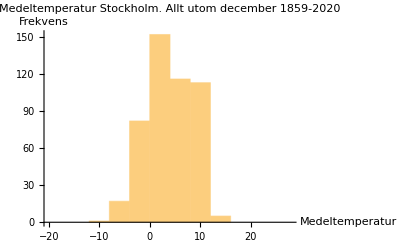

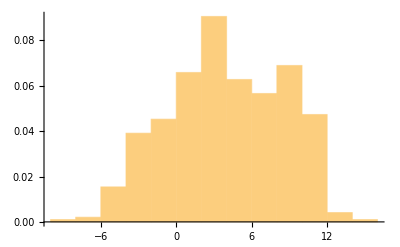

```mathematica
allaMånaderUtomDec = Append[{},{mar,apr,maj}];
allaMånaderUtomDecKorrekt = Flatten[allaMånaderUtomDec];
Length[allaMånaderUtomDecKorrekt]
marAprMaj =allaMånaderUtomDecKorrekt;
Total[marAprMaj]/Length[marAprMaj]
temperaturintervallet= {-20,30,4};
minst = Sort[marAprMaj];
störst = Sort[marAprMaj];
minst[[1]]
störst[[Length[marAprMaj]-1]]

Show[Histogram[marAprMaj,temperaturintervallet, AxesLabel->{"Medeltemperatur", "Frekvens"}],PlotLabel->"Medeltemperatur Stockholm. Allt utom december 1859-2020"]
Show[Histogram[marAprMaj,Automatic,"ProbabilityDensity"],Plot[PDF[ℋ["FittedDistribution"],x],{x,-20,20},PlotStyle->Thick, PlotRange->{0,20}]]
```

```mathematica
"Hitta element inom ett spann med månaderna dec, jan, feb  åren 1859-2020" ;
k1 = Length[Select[viMånader,#<-11&]]
k2 = Length[Select[viMånader,-8>#>=-11&]]
k3 = Length[Select[viMånader,-5>#>=-8&]]
k4 = Length[Select[viMånader,-2>#>=-5&]]
k5 = Length[Select[viMånader,1>#>=-2&]]
k6 = Length[Select[viMånader,#>=1&]]
k1+k2+k3+k4+k5+k6
Length[våMånader]
Total[våMånader]/Length[våMånader]
```

5

16

65

157

194

49

486

486

3.97922

486

3.97922

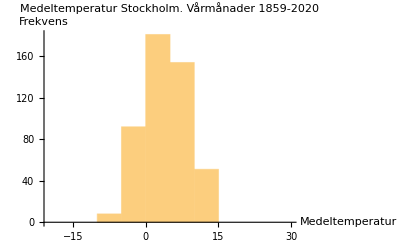

-Graphics-

```mathematica
allaMånaderUtomDec = Append[{},{mar,apr,maj}];
allaMånaderUtomDecKorrekt = Flatten[allaMånaderUtomDec];
Length[allaMånaderUtomDecKorrekt]
marAprMaj =allaMånaderUtomDecKorrekt;
Total[marAprMaj]/Length[marAprMaj]
temperaturintervallet= {-20,30,5};
Show[Histogram[marAprMaj,temperaturintervallet, AxesLabel->{"Medeltemperatur", "Frekvens"}],PlotLabel->"Medeltemperatur Stockholm. Vårmånader 1859-2020"]
Show[Histogram[marAprMaj,Automatic,"ProbabilityDensity"],Plot[PDF[ℋ["FittedDistribution"],x],{x,-20,20},PlotStyle->Thick, PlotRange->{0,20}]]
```

486

-2.48313

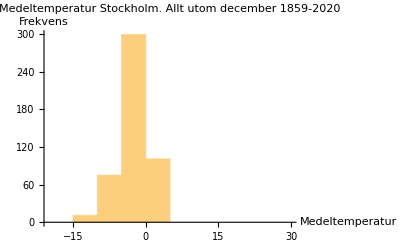

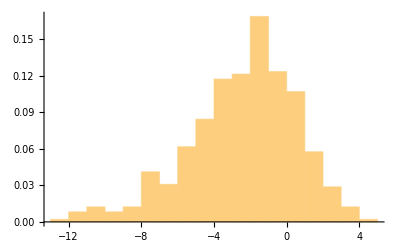

```mathematica
allaMånaderUtomDec = Append[{},{dec,jan,feb}];
allaMånaderUtomDecKorrekt = Flatten[allaMånaderUtomDec];
Length[allaMånaderUtomDecKorrekt]
Total[allaMånaderUtomDecKorrekt]/Length[allaMånaderUtomDecKorrekt]
temperaturintervallet= {-20,30,5};
Show[Histogram[allaMånaderUtomDecKorrekt,temperaturintervallet, AxesLabel->{"Medeltemperatur", "Frekvens"}],PlotLabel->"Medeltemperatur Stockholm. Allt utom december 1859-2020"]
Show[Histogram[allaMånaderUtomDecKorrekt,Automatic,"ProbabilityDensity"],Plot[PDF[ℋ["FittedDistribution"],x],{x,-20,20},PlotStyle->Thick, PlotRange->{0,20}]]
```

```mathematica
Mars, April, Maj 
lägst: -8.9
högst: 14.8

December, Januari, Februari
lägst: -12.2
högst: 4.3
```

```mathematica
Spannvidd = 7*5 =28
"(-∞,-6)+[-6,-3)+[-3,0)+[0,3)+[3,6)+[6,9)+[9,∞)"

"
K = 6
(-∞,-4)+[-4,0)+[0,4)+[4,8)+[8,12)+[12,∞)"
```

```mathematica
"Mars, April, Maj 
lägst: -8.9
högst: 14.8
Spannvid: 14.8-(-8.9)= 23.7
(-∞,-4)+[-4,0)+[0,4)+[4,8)+[8,12)+[12,∞)"
```

```mathematica
"December, Januari, Februari
lägst: -12.2
högst: 4.3 
Spannvid: 23,7
(-∞,-4)+[-4,0)+[0,4)+[4,8)+[8,12)+[12,∞)"
```

```mathematica
"Hitta element inom ett spann med månaderna mar, apr, maj åren 1859-2020
I_k=5" ;
k1 = Length[Select[våMånader,#<-4&]]
k2 = Length[Select[våMånader,0>#>=-4&]]
k3 = Length[Select[våMånader,4>#>=0&]]
k4 = Length[Select[våMånader,8>#>=4&]]
k5 = Length[Select[våMånader,12>#>=8&]]
k6 = Length[Select[våMånader,#>=12&]]
k1+k2+k3+k4+k5+k6;
Length[viMånader];
Total[viMånader]/Length[viMånader];
```

18

82

152

116

113

5

```mathematica
"Beräkna ϕ-värdena för den ickestandardiserade normalfördelningen för:
* Vårmånaderna"
```

```mathematica
"Hur man beräknar ϕ-värdena för en icke-standardiserad normalfördelning: (x - μ)/σ"
```

```mathematica
(-4-(3.9792181069958854))/4.546706092832403
(0-(3.9792181069958854))/4.546706092832403
(4-(3.9792181069958854))/4.546706092832403
(8-(3.9792181069958854))/4.546706092832403
(12-(3.9792181069958854))/4.546706092832403
```

-1.75494

-0.875187

0.00457076

0.884329

1.76409

```mathematica
1- ϕ(1.7549)=1-0.9599= 0.0401
1-ϕ(0.87518)=...
ϕ(0.004)=0.50
ϕ(0.8843)=...
ϕ(1.7640)=...
```

```mathematica
"Hur man beräkna ϕ-värdena för en icke-standardiserad normalfördelning med en funktion"
```

```mathematica
Clear[x]
NProbability[x<=-4,x\[Distributed]NormalDistribution[3.9792181069958854,4.546706092832403]]
Clear[x]
NProbability[x<=0,x\[Distributed]NormalDistribution[3.9792181069958854,4.546706092832403]]
Clear[x]
NProbability[x<=4,x\[Distributed]NormalDistribution[3.9792181069958854,4.546706092832403]]
Clear[x]
NProbability[x<=8,x\[Distributed]NormalDistribution[3.9792181069958854,4.546706092832403]]
Clear[x]
NProbability[x<=12,x\[Distributed]NormalDistribution[3.9792181069958854,4.546706092832403]]
Clear[x]
```

0.0396344

0.190736

0.501823

0.811741

0.961141

```mathematica
"Beräkna arean inuti de utstakade intervallen:  
0.19073-0.03963 = 0.1511
0.50182-0.19073  = 0.31109
0.81174 -0.50182 = 0.30992
0.96114-0.81174 = 0.1494
1-0.96114 = 0.0388 "
```

```mathematica
0.19073-0.03963 
0.50182-0.19073
0.81174 -0.50182
0.96114-0.81174 
1-0.96114
```

0.1511

0.31109

0.30992

0.1494

0.03886

```mathematica
"Beräkna de förväntade antalet tal inom ett intervall:
486*0.03963 = ...
486*0.1511 = ...
486*0.31109 = ...
486*0.3099 = ...
486*0.1494 = ...
486*0.03886 = ..."
```

```mathematica
486*0.03963
486*0.1511
486*0.31109
486*0.3099
486*0.1494
486*0.03886
```

19.2602

73.4346

151.19

150.611

72.6084

18.886

```mathematica
"Faktiska antalet per intervall:
k1 = 18
k2 = 82
k3 = 152
k4= 116
k5= 113
k6= 5
Obs. både summan av de observerade och förväntade talen ska bli 486 om beräkningarna är utförda på korrekt vis"
```

```mathematica
"Beräkna χ^2=∑((observerad - förväntad)^2/förväntad  )"
```

```mathematica
observeradeVår = {18,82,152,116,113,5}
förväntadeVår = {19.2601,73.4346,151.1897,150.6114,72.6084,18.8859}
∑_(i=1)^Length[observeradeVår] (  (observeradeVår[[i]]-förväntadeVår[[i]])^2/förväntadeVår[[i]])
```

{18,82,152,116,113,5}

{19.2601,73.4346,151.19,150.611,72.6084,18.8859}

41.719

```mathematica
"Hypotes
1.Hypotes
H_0: Fördelningen är normalfördelad
H_1: Fördelningen är ej normalfördelad

2. Signifikans α = 0.05
3. Test statistik: 
χ^2=∑((observerad - förväntad)^2/förväntad  = 351.8503
df = k - p (antal parametrar; i vårt fall medelvärdet och standardavvikelsen)-1 = 7 -2 -1 = 4
df = 4

Enligt Järpe är antelet frihetsgrader (df) för normalfördelningen: 
df = K-1 = 7-1 = 6

4. Kritiska värden: desto längre ifrån noll desto längre ifrån hypotesen (att H_0 är normalfördelad
)
Vilket blir i  χ^2-percentilerns lista blir: 
(χ^2)_(α, df)=(χ^2)_(0.05, 6)=12.5916

5. H_0 förkastas då signifikansen är 5%, således antas H_1:
u> (χ^2)_(α, df)
41.7189>12.5916

Detta betyder inte att talen inte är normalfördelade, endast att det saknas fler observationer"
```

```mathematica
"
K =5
December, Januari, Februari
lägst: -12.2
högst: 4.3 
Spannvid: 16,5
(-∞,-9)+[-9,-5)+[-5,-1)+[-1,3)+[3,∞)"
```

```mathematica
"Hitta element inom ett spann med månaderna dec, jan, feb  åren 1859-2020
I_k=5" ;
k1 = Length[Select[viMånader,#<-9&]]
k2 = Length[Select[viMånader,-5>#>=-9&]]
k3 = Length[Select[viMånader,-1>#>=-5&]]
k4 = Length[Select[viMånader,3>#>=-1&]]
k5 = Length[Select[viMånader,#>=3&]]
k1+k2+k3+k4+k5
Length[våMånader];
Total[våMånader]/Length[våMånader];
```

15

71

239

154

7

486

```mathematica
"Beräkna ϕ-värdena för den ickestandardiserade normalfördelningen för:
* Vintermånaderna"
"Hur man beräknar ϕ-värdena för en icke-standardiserad normalfördelning: (x - μ)/σ"
```

```mathematica
(-9-(-2.4831275720164614))/2.968147621197032
(-5-(-2.4831275720164614))/2.968147621197032
(-1-(-2.4831275720164614))/2.968147621197032
(3-(-2.4831275720164614))/2.968147621197032
```

-2.1956

-0.847961

0.499681

1.84732

```mathematica
1- ϕ(2.195)=1-0.9857= 0.0143
1- ϕ(0.847)=...
ϕ(0.499)=...
ϕ(1.847)=0.9671
```

```mathematica
"Hur man beräkna ϕ-värdena för en icke-standardiserad normalfördelning med en funktion"
```

```mathematica
Clear[x]
NProbability[x<=-9,x\[Distributed]NormalDistribution[-2.4831275720164614,2.968147621197032]]
Clear[x]
NProbability[x<=-5,x\[Distributed]NormalDistribution[-2.4831275720164614,2.968147621197032]]
Clear[x]
NProbability[x<=-1,x\[Distributed]NormalDistribution[-2.4831275720164614,2.968147621197032]]
Clear[x]
NProbability[x<=3,x\[Distributed]NormalDistribution[-2.4831275720164614,2.968147621197032]]
```

0.0140602

0.19823

0.69135

0.96765

```mathematica
"Beräkna arean inuti de utstakade intervallen:  
0.014060
0.19822-0.014060  = ...
0.6913 -0.19822= ...
0.96764-0.6913 = ...
1-0.96764 = ... "
```

```mathematica
0.19822-0.014060  
0.6913 -0.19822
0.96764-0.6913 
1-0.96764
```

0.18416

0.49308

0.27634

0.03236

```mathematica
"Beräkna de förväntade antalet tal inom ett intervall:
486*0.03963 = ...
486*0.1511 = ...
486*0.31109 = ...
486*0.3099 = ...
486*0.1494 = ...
486*0.03886 = ..."
```

```mathematica
486*0.014060
486*0.18416
486*0.49308
486*0.27634
486*0.03236
```

6.83316

89.5018

239.637

134.301

15.727

```mathematica
"Faktiska antalet per intervall:
k1 = 7
k2 = 71
k3 = 239
k4= 154
k5= 15
Obs. både summan av de observerade och förväntade talen ska bli 486 om beräkningarna är utförda på korrekt vis"
```

```mathematica
"Beräkna χ^2=∑((observerad - förväntad)^2/förväntad  )"
```

```mathematica
observeradeVår = {7,71,239,154,15}
förväntadeVår = {6.83315,89.50175,239.6368,134.30124,15.7269}
∑_(i=1)^Length[observeradeVår] (  (observeradeVår[[i]]-förväntadeVår[[i]])^2/förväntadeVår[[i]])
```

{7,71,239,154,15}

{6.83315,89.5018,239.637,134.301,15.7269}

6.75337

```mathematica
"Hypotes
1.Hypotes
H_0: Det går inte att bevisa att populationen inte är normalfördelad
H_1: Fördelningen är ej normalfördelad
H_0: F_x = F_0
H_1: F_x ≠ F_0

2. Signifikans α = 0.05
3. Test statistik: 
χ^2=∑((observerad - förväntad)^2/förväntad  = 20.32468
df = k - p (antal parametrar; i vårt fall medelvärdet och standardavvikelsen)-1 = 5 -2 -1 = 2
df = 2
df = (<antal rader i korstabell> -1)(<antal kolumner i korstabell> )

Enligt Järpe är antelet frihetsgrader (df) för normalfördelningen: 
df = K-1 = 6-1 = 5

4. Kritiska värden: desto längre ifrån noll desto längre ifrån hypotesen (att H_0 är normalfördelad
)
Vilket blir i  χ^2-percentilerns lista blir: 
(χ^2)_(α, df)=(χ^2)_(0.05, 5)=11.0705

5. H_0 är sann då funktionsvärdet (d.v.s. u) är större än percentilvärdet för chi-två-testet, således antas A_α för när signifikansen är 5%:
u> (χ^2)_(α, df)
6.7533<11.0705

Detta betyder inte att talen inte är normalfördelade, endast att det saknas fler observationer"
```

```mathematica
8. p-värdet = α så att Subscript[χ, α,K-1]^2= u (för χ-två-test)
I detta fallet får man göra två intervall enligt: 
Subscript[χ, α2]^2<u<Subscript[χ, α1]^2
då K = 6-1 = 5 
är: 
Subscript[χ, 0.25,5]^2<u<Subscript[χ, 0.10,5]^2= 6.6257< 6.7533 < 9.2364


"P-värdet är det lägsta signifikansvärdet man hade kunnat förkasta på med det
*U-värdet (tesftunktionens värde) 
för testet

Förkasta H_0 då p-värdet ligger inom det kritiska området "
```

```mathematica
"Det går aldrig att bevisa att det är en viss fördelning, men däremot kan man kontrollera att det inte går att bevisa att det inte är en viss fördel"
```

```mathematica
"Testvilkoret: 
A_α={u > χ_α^2(K-1)}
Säger att: 
* testfunktionensvärde (d.v.s. u) ska vara större än percentilvärdet för chi-två-testet"
```

```mathematica
"Helst när man gör ett chi-två-test ska det vara lika många klasser som:
* 1/5 av observationerna N, d.v.s. 486/5"
```

```mathematica
"Konfidenintervallet i vårt fall handlar om att man:
sätter två gränser inom vilka man uppskattar att väntevärdet ska finnas

Då skattningen av väntevärdet, E(θ^(X1,X2,...Xn)) är exakt på prick det faktiska väntevärdet , d.v.s. E(θ^(X1,X2,...Xn)) = θ, är skattningen väntevärdesriktig"
```

```mathematica
"Percentilerna används i konfidensintervall och hypoteserna för att sätt ett x-värde så att en bestämd procentenenhet finns bortom x-värdet "
```

```mathematica
"Vad är ett konfidensintervall: 
* man gör en skattning av exv. variansen, väntevärdet och sannolikheten att den hamnar inom ett par gränser
Om man har fler observationer är sannolikheten större att man inte behöver välja en högre konfidensgrad (d.v.s. skapad ett större spann).
Man kan spekulera i om man har tillräckligt med observationer om resultatet av en konfidensintervallsberäkning inte blir som tänkt

*P(L<= θ <= U) = 1 - α 
är sannolikheten att parametern θ ligger inom gränserna  

Obs. avrunda den undre gränsen 
* nedåt
och den övre gränsen:
* uppåt"
```

```mathematica
xMedVin = Total[viMånader]/Length[viMånader]
s1Vin =√(1/(vin-1)*(∑_(i=1)^vin (viMånader[[i]]^2)-(vin*viMedel^2)))
```

-2.48313

2.96815

```mathematica
xMedVin - (1.959964* 2.968147621197032/(√486))
xMedVin + (1.959964* 2.968147621197032/(√486))
```

-2.74701

-2.21924

```mathematica
xMedVår =Total[våMånader]/Length[våMånader]
s1 =√(1/(vån-1)*(∑_(i=1)^vin våMånader[[i]]^2-(vån*våMedel^2)))
```

3.97922

4.54671

```mathematica
xMedVår- (1.959964* 4.546706092832403/(√486))
xMedVår+ (1.959964*  4.546706092832403/(√486))
```

3.57499

4.38345

```mathematica
n = 486
```

```mathematica
"Då stickprovsvariansen, \sigma^2, är kända för stickproven kan beräknas konfidensintervallet enligt: "
```

```mathematica
"Med hypotestest är det tänkt att man ska:
* kunna utala sig om framtiden med hjälp av känd data/kända observationer "
```

```mathematica
"Man kan i metoden förkasta själva hypotesen"
"i resultatet kan man tolka själva resultatet (förkasta eller inter förkasta) och vad det innebär för området och om det finns andra områden som bygger vidare från det här (andra undersökningar?)"
```

```mathematica
"Varför gör man hypotestest:
Det kan ibland tyckas “uppenbart” att något har effekt.

Men det kan vara svårt att skilja slumpmässig avvikelse
från vad som är systematisk effekt.

Och med komplexa system kan effekter bli än mer
dolda.

Så för att konsekvent och välgrundat kunna bedöma
effekter av analys och signifikans av modeller
behövs metodik för diskriminering mellan slump och
effekt och kunskap om hur man bör gå till väga."
```

```mathematica
"Hur gör man ett hypotestest: 
1. Planering
Kausalitetssamband, enkätfrågor, kostnader,
stickprovsstorlek, etc.
2. Analys
Hypoteser, jämförelse av testfunktionsvärde med
percentil, redovisning av utfall, p-värde.
3. Resultat
Slutsats, konsekvenser och post-hoc-metoder
"
```

```mathematica
"Arbetsgång för hypotestest:
```

```mathematica
"Producera ett hypotest då σ.b2 är känd
```

```mathematica
"Procedur för hypotestestet då σ.b2 är okänd
```

```mathematica
"P-värdet är det lägsta signifikansvärdet man hade kunnat förkasta på med det
*U-värdet (tesftunktionens värde) 
för testet

Förkasta H_0 då p-värdet ligger inom det kritiska området "
```

```mathematica
"Beräkna jämförelsen av medelvärden: 
((x̄)_1)/(√(s_2^2/n_1))
1. stickproven 
viMedel
våMedel 
2. hypoteserna 

Eftersom vi vill veta om det finns någon skillnad mellan medelvärdesstickproven använder vi fall "C"
3. signifikansnivån 
α
4. Testfunktionerna 
U = ((x̄)_1)/(√(s_2^2/n_1))
Detta då n>30
5. Villkor 
* A = A_α = u < −t_(α,  n1 + n2 -2)
* B = A_α = u > t_(α,  n1  +  n2  - 2)
* C = A_α = |u| > t_(α/2,  n1 + n2 -2)

I detta fallet väljer vi fall "C" beroende på valet av hypotesen "C"
Där :
* n1 + n2 -2
är df (degrees of freedom); frihetsgraderna 
6. Förkasta A_α, inte annars "
```

```mathematica
x1 = Total[Flatten[{dec,jan,feb}]]/Length[Flatten[{dec,jan,feb}]]
x2 = Total[Flatten[{mar,apr,maj}]]/Length[Flatten[{mar,apr,maj}]]
st1 =1/(vån-1)*(∑_(i=1)^vin våMånader[[i]]^2-(vån*våMedel^2)) 
st2 = 1/(vin-1)*(∑_(i=1)^vin viMånader[[i]]^2-(vin*viMedel^2))
n1 = Length[Flatten[{dec,jan,feb}]]
n2 = Length[Flatten[{mar,apr,maj}]]
a = 0.05
U = (x1-x2)/(√(st1/n1+st2/n2))
"Aa = A_α = |u| > t_(α/2,  n1 + n2 -2)= 26.2377 > t_(0.05/2,  486 + 486 -2)
= 26.2377 > t_(0.025,  970)
= 26.2377 > 0.6770";
```

-2.48313

3.97922

20.6725

8.8099

486

486

0.05

-26.2378

```mathematica
TTest[{Flatten[{dec,jan,feb}],Flatten[{mar,apr,maj}]}];
```

TTest::nortst: At least one of the p-values in {2.63825×10^-6,0.0000777241}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

```mathematica
"Följande funktion 'Standardaize'  standardiserar varje enskilt värde enligt i listan enligt: 
(x - μ)/σ
(-3.2 - (-2.4831))/2.9681476211970";
Clear[data1]
Clear[data2]
data1 = Standardize[Flatten[{dec,jan,feb}]];
data2 = Standardize[Flatten[{mar,apr,maj}]];
Length[data1]
Length[data2]
(-3.2-(-2.4831))/2.9681476211970;
TTest[{data1,data2}]//N
TTest[{Standardize[Flatten[{dec,jan,feb}]],Standardize[Flatten[{mar,apr,maj}]]}]//N
```

486

486

TTest::nortst: At least one of the p-values in {2.63825×10^-6,0.0000777241}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

1.

TTest::nortst: At least one of the p-values in {2.63825×10^-6,0.0000777241}, resulting from a test for normality, is below 0.025. The tests in {T} require that the data is normally distributed.

1.

```mathematica
"Följande funktion standardiserar varje enskilt värde enligt: \\n(x - μ)/σ\\n(-3.2 - (-2.483127572016461))/8.80990030121";
```

```mathematica
data=RandomVariate[NormalDistribution[0.05,1],10^2]
```

{0.843397,0.394513,0.769458,-1.67038,-0.237871,-1.37724,-1.25838,0.597491,-0.219955,-1.19458,-0.021147,-0.0319812,-0.412582,-0.011714,-1.22919,-0.309248,1.93623,-0.754317,0.724196,-1.21636,-0.644145,0.30107,1.12583,-0.698599,0.17025,0.13668,-0.337802,0.951681,-0.307737,-1.83015,-0.966073,0.562223,1.84901,-2.04842,0.509756,0.962481,0.0826305,-1.43743,0.687153,1.00143,0.0205712,1.95485,0.163607,-0.132524,0.630037,1.0329,0.103431,0.856062,2.22116,3.01939,-0.841503,-0.494928,-1.05692,1.17578,1.3752,2.09005,1.38254,-1.09216,-1.91601,-0.124218,0.00977908,0.235987,-0.259375,1.92951,0.68363,0.570784,-0.803732,2.33956,0.528904,-0.303771,0.293033,0.267317,-1.34312,-0.546269,-0.179954,0.937406,0.2103,2.04689,0.745722,0.46104,0.652545,-0.524651,1.37285,-1.54632,-0.396605,-0.38701,-0.0708446,-0.134266,1.81464,-0.0155606,-1.25298,-0.352754,0.411651,0.162235,-0.433131,-1.03139,-0.538975,-0.491531,0.196922,-0.80052}

```mathematica
TTest[data]
```

0.325775

```mathematica
square[x_]:=x^2;
SetAttributes[square,Listable]
listas = {21.7,19.8,22,21.6,20.5,19,21.5,22.3,21.5,26.3,21,18.7,17.7,23.8,20.1,19,22.1,20.9,20.8,21.1,19.4}
kvaLista = square[listas]//N
Total[kvaLista]
```

{21.7,19.8,22,21.6,20.5,19,21.5,22.3,21.5,26.3,21,18.7,17.7,23.8,20.1,19,22.1,20.9,20.8,21.1,19.4}

{470.89,392.04,484.,466.56,420.25,361.,462.25,497.29,462.25,691.69,441.,349.69,313.29,566.44,404.01,361.,488.41,436.81,432.64,445.21,376.36}

9323.08

```mathematica
"Konfidensintervall för jämförelse av populationsmedelvärden, μ_x

((x̄)_1-(x̄)_2)±√(s_2^2/n_1)"
```

```mathematica
v1Vin =1/(vin-1)*(∑_(i=1)^vin (viMånader[[i]]^2)-(vin*viMedel^2))
v1Vår =1/(vån-1)*(∑_(i=1)^vin våMånader[[i]]^2-(vån*våMedel^2))
```

8.8099

20.6725

```mathematica
NumberForm[v1Vår,16]
```

20.6725362945993

```mathematica
våMedel
viMedel
(våMedel-viMedel)+1.644854*√(v1Vår/468+v1Vin/468)
(våMedel-viMedel)-1.644854*√(v1Vår/468+v1Vin/468)
(viMedel-våMedel)+1.644854*√(v1Vår/468+v1Vin/468)
(viMedel-våMedel)-1.644854*√(v1Vår/468+v1Vin/468)
```

3.97922

-2.48313

6.87519

6.0495

-6.0495

-6.87519